```mathematica
(*piecewise linearization with refractory period added*)
```

```mathematica
2(1000-177/615)/534.5
```

3.74074

```mathematica
2(500-eIth/ce)/244.362989341
```

4.08897

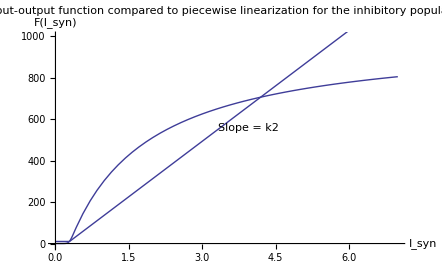

```mathematica
Show[refi1,refi2]
```

```mathematica
Show[refe1,refe2]
```

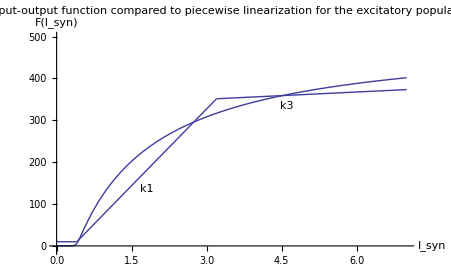

```mathematica
ke=244.3629893/2;  ki=534.5/2;
```

```mathematica
(*for constant slope*)
```

```mathematica
c1=a (ce(Is+Io)-eIth);c2=a ce Jee; c3=a ce Jie;c4= ci Io-iIth;c5=ci Jei;c6=ci Jii;c9=k1 c3 k2 c2/(1/ti+k2 c6-k1 c2); c10=k1 c2 -1/te -k1 c1 +(c4-c2)k1 c3 k2 /(1/ti +k2 c6); c11=k1 c1-k1 c3 k2 c4/(1/ti +k2 c6);
```

```mathematica
Se=(-c10+Sqrt[c10 ^2-4 c9 c11])/(2 c9)
```

```mathematica
(*for middle region, excitatory*)
c1=a (ce(Is+Io)-eIth);c2=a ce Jee; c3=a ce Jie;c4= ci Io-iIth;c5=ci Jei;c6=ci Jii;c9=ke c3 ki c2/(1/ti+ki c6-ke c2); c10=ke c2 -1/te -ke c1 +(c4-c2)ke c3 ki /(1/ti +ki c6); c11=ke c1-ke c3 ki c4/(1/ti +ki c6); Se=(-c10+Sqrt[c10 ^2-4 c9 c11])/(2 c9);
```

```mathematica
Solve[eIth/ce==Jee Se-Jie (1/c3(c1+c2 Se-Se/(te  k1(1-Se))))+Is+Io]
```

{{Se→-3.71572×10^12},{Se→-1.00923×10^-13}}

```mathematica
(ce (eIth/ce+4.09)  -eIth)/(1-Exp[-g(ce (eIth/ce+4.09)  -eIth)]+tre/1000(ce(eIth/ce+4.09)-eIth)  )
```

358.589

```mathematica
(*upper bound for Se -> 0.9978260582226827*)
358.589*a/(1/tre+a 358.589)
```

0.997826

```mathematica
(*lower bound for Se: 0 to Se->0.99989, *)
```

```mathematica
Io=.2; Jie=0.93; Jii=0.035; Jee=0.8371975189912353;
```

```mathematica
Solve[1/te-k1 c2 +2 k1 c2 Se+1/ti +k2 c6==0]
```

{{Jee→-0.258416},{Jee→0.837198}}

```mathematica
Clear[Se]
```

```mathematica
Si2=1/c3(c1+c2 Se-Se/(te  k1(1-Se)));
```

```mathematica
Si1=k2(c4+c2 Se)/(1/ti + k2 c6);
```

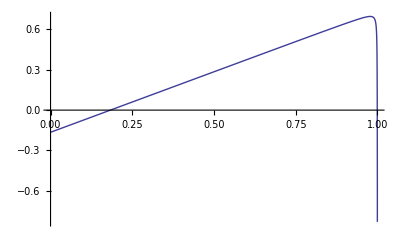

```mathematica
pw1=Plot[Si2,{Se,0,1}]
```

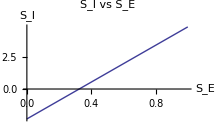

```mathematica
pw2=Plot[Si1,{Se,0,1},PlotLabel->"S_I vs S_E",AxesLabel->{"S_E","S_I"}]
```

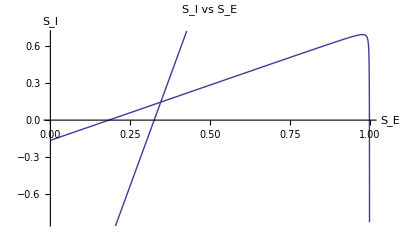

```mathematica
Show[pw1,pw2,PlotLabel->"S_I vs S_E",AxesLabel->{"S_E","S_I"}]
```

```mathematica
D[1/c3(c1+c2 Se-Se/(te  k1(1-Se))),Se]
```

(c2-1/(k1 (1-Se) te)-Se/(k1 (1-Se)^2 te))/c3

```mathematica
Clear[c1,c2,c3,te,k1,Se]
```

```mathematica
Solve[1/c3(c1+c2 Se-Se/(te  k1(1-Se)))==k2(c4+c2 Se)/(1/ti + k2 c6)]
```

{{Se→0.3457},{Se→1.00011}}